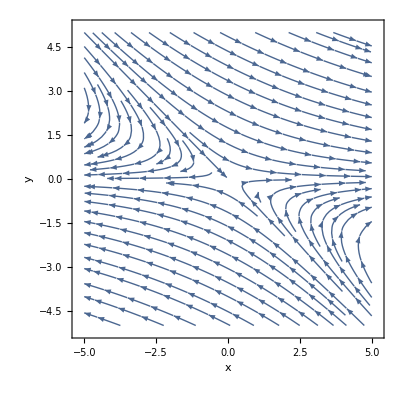

```mathematica
(*Problem 8*)
(*a*)
f[x_,y_]:=x + 2*y;
g[x_,y_]:=-y;
StreamPlot[{f[x,y],g[x,y]},{x,-5,5},{y,-5,5},FrameLabel->{x,y}]
```

x y (x+y)

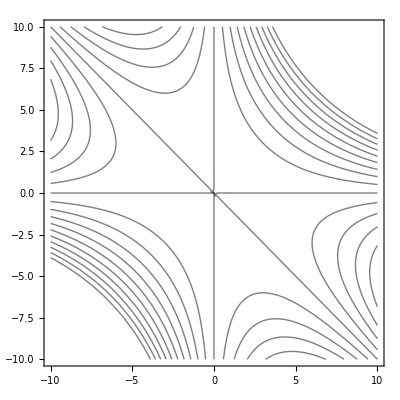

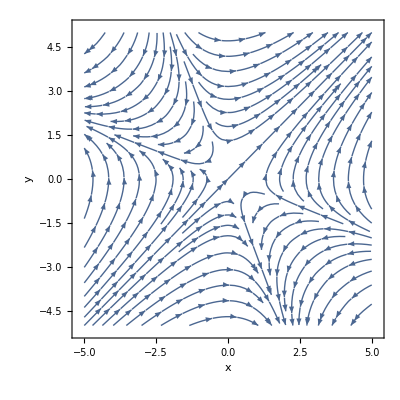

```mathematica
(*b*)
(*b*)
H =x*y*(x+y)
ContourPlot[H,{x,-10,10},{y,-10,10},ContourShading->False,Contours->20]
f[x_,y_]:=y^2+ 2*x*y;
g[x_,y_]:=x^2 + 2*x*y;
StreamPlot[{f[x,y],g[x,y]},{x,-5,5},{y,-5,5},FrameLabel->{x,y}]
```

x (x-y) y

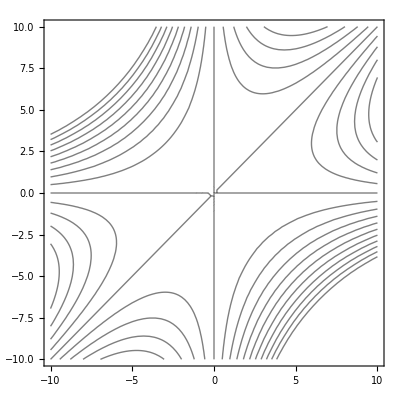

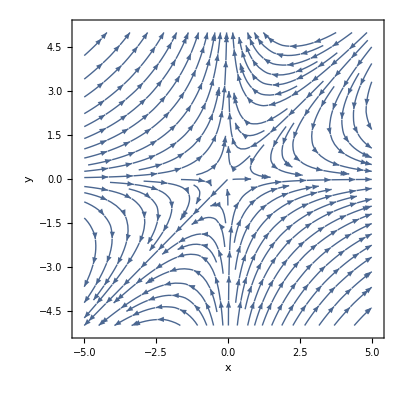

```mathematica
(*c*)
H =x*y*(x-y)
ContourPlot[H,{x,-10,10},{y,-10,10},ContourShading->False,Contours->20]
f[x_,y_]:=x^2-2*x*y;
g[x_,y_]:=y^2 - 2*x*y;
StreamPlot[{f[x,y],g[x,y]},{x,-5,5},{y,-5,5},FrameLabel->{x,y}]
```

-x^2 y+1/3 (x^3+y^3)

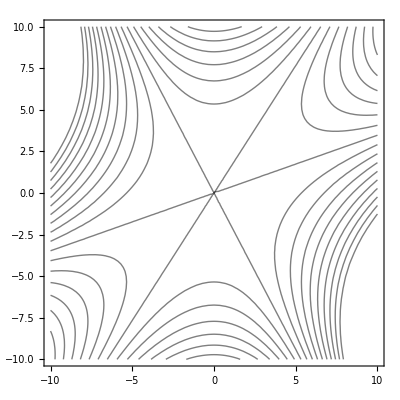

```mathematica
(*d*)
H =(x^3 + y^3)/3 - x^2 * y
ContourPlot[H,{x,-10,10},{y,-10,10},ContourShading->False,Contours->20]
```

Cos[y] Sin[x]^2

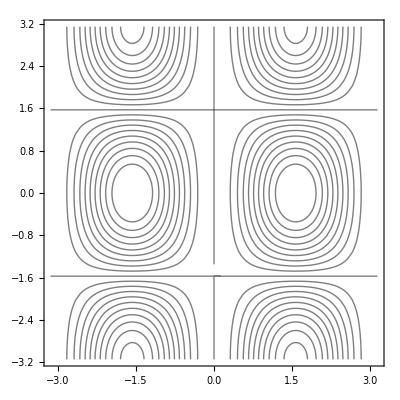

```mathematica
(*d*)
H =Sin[x]^2*Cos[y]
ContourPlot[H,{x,-Pi,Pi},{y,-Pi,Pi},ContourShading->False,Contours->20]
```

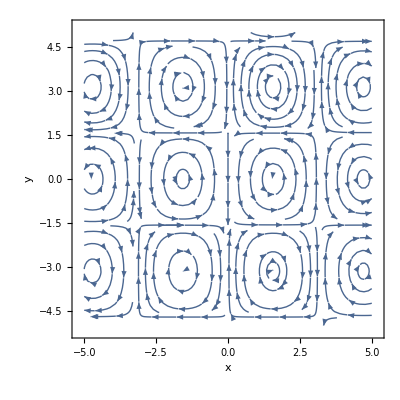

```mathematica
f[x_,y_]:=-Sin[x]^2*Sin[y]
g[x_,y_]:=-2*Sin[x]*Cos[x]Cos[y];
StreamPlot[{f[x,y],g[x,y]},{x,-5,5},{y,-5,5},FrameLabel->{x,y}]
```

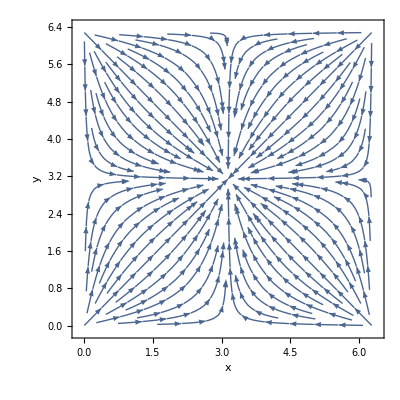

```mathematica
(*Problem 12*)
f[x_,y_]:=Sin[x];
g[x_,y_]:=Sin[y];
StreamPlot[{f[x,y],g[x,y]},{x,0,2*Pi},{y,0,2*Pi},FrameLabel->{x,y}]
```

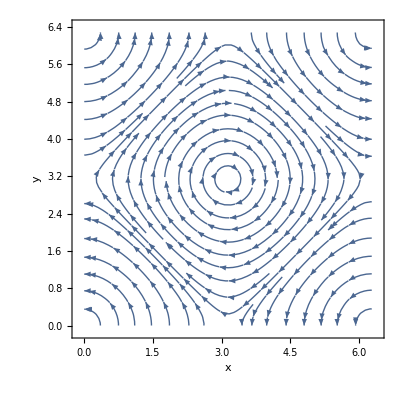

```mathematica
f[x_,y_]:=-Sin[y];
g[x_,y_]:=Sin[x];
StreamPlot[{f[x,y],g[x,y]},{x,0,2*Pi},{y,0,2*Pi},FrameLabel->{x,y}]
```